# Inlämningsuppgift 1: Probelmlösning

## Polynomekvation

Nedan kommer vi att demostera två stycen lösningar till följande polynom: x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2=0

### Lösning ett

Här följer en lösning med hjälp av Wolfram Alpha.

Solve (x^5 - 2*x^4 - (19/4)*x^3 + (31/4)*x^2 + (11/2)*x - 15/2 = 0)

WolframAlphaQueryResults

### Lösning två

Här följer en lösning med hjälp av Mathematicas olika funktioner.

```mathematica
f[x_] =x^5 - 2*x^4 - (19/4)*x^3 + (31/4)*x^2 + (11/2)*x - 15/2
```

-15/2+(11 x)/2+(31 x^2)/4-(19 x^3)/4-2 x^4+x^5

```mathematica
{x1, x2, x3, x4, x5} = x/.Solve [f[x] ==0, x]
```

{-3/2,1,5/2,-√2,√2}

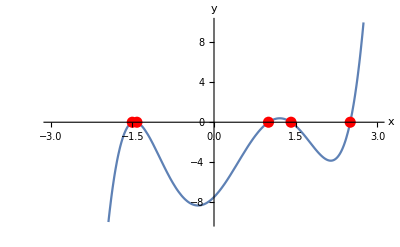

```mathematica
p1 = Plot [f[x],{x,-10, 10},
PlotRange -> {{-3,3}, {-10,10}},
AxesLabel-> {"x", "y"},
Epilog->{PointSize[0.02],Red, Point[{{x1, f[x1]},{x2, f[x2]}, {x3, f[x3]}, {x4, f[x4]}, {x5, f[x5]}}]}]
```

## Ekvation med abslout belopp

Nedan följer en lösning till abslutbeloppet |x-1|+|x+2|=3

```mathematica
Reduce [Abs[x - 1] + Abs[x + 2] == 3, x, Reals]
```

-2≤x≤1

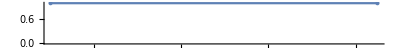

```mathematica
NumberLinePlot[-2≤x≤1,x]
```

Källor: 
Solve 
["http://reference.wolfram.com/language/ref/Solve.html"](http://reference.wolfram.com/language/ref/Solve.html)

Ekvationer med absolutbelopp
https://www.wolframalpha.com/input/?i=%5BAbs%5Bx+-+1%5D+%2B+Abs%5Bx+%2B+2%5D+%3D%3D+3,+x,+Reals%5D

## Binomiska ekvation

```mathematica
g[z_] ==z^7 == 1 - I
```

g[x_]==z^7==1-ⅈ

```mathematica
{z1,z2, z3, z4,z5, z6, z7}= z /. Solve [z^7 == 1 - I, z]
```

{(1-ⅈ)^(1/7),-(-1)^(1/7) (1-ⅈ)^(1/7),(-1)^(2/7) (1-ⅈ)^(1/7),-(-1)^(3/7) (1-ⅈ)^(1/7),(-1)^(4/7) (1-ⅈ)^(1/7),-(-1)^(5/7) (1-ⅈ)^(1/7),(-1)^(6/7) (1-ⅈ)^(1/7)}

```mathematica
p1 = Plot [g[z],{z,-10, 10},
PlotRange -> {{-3,3}, {-10,10}},
AxesLabel-> {"Re", "Im"},
Epilog->{PointSize[0.02],Red, Point[{{z1, f[z1]},{z2, f[z2]}, {z3, f[z3]}, {z4, f[z4]}, {z5, f[z5]},{z6 ,f[z6]},{z7, f[z7]}}]}]
```

-Graphics-

```mathematica
ListPlot[g[x], AxesLabel->{"Re", "Im"}, AspectRatio->Automatic,PlotMarkers->{Automatic, Medium},Epilog->{ EdgeForm[Red],FaceForm[],Rectangle[{g[x][[3,1]], g[x][[3,2]]}, {g[x][[2, 1]], g[x][[2, 2]]}], }]
```